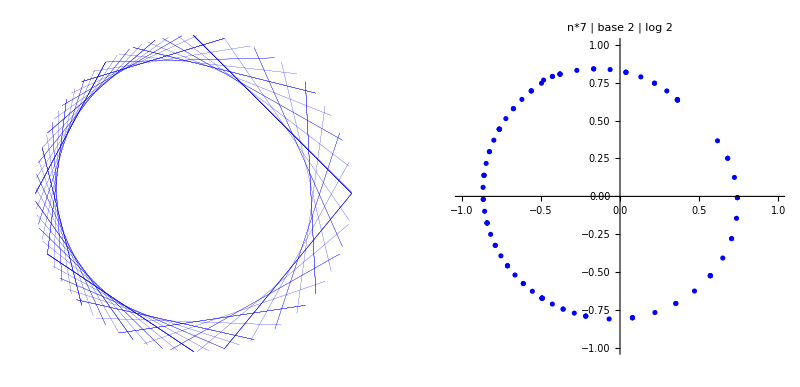

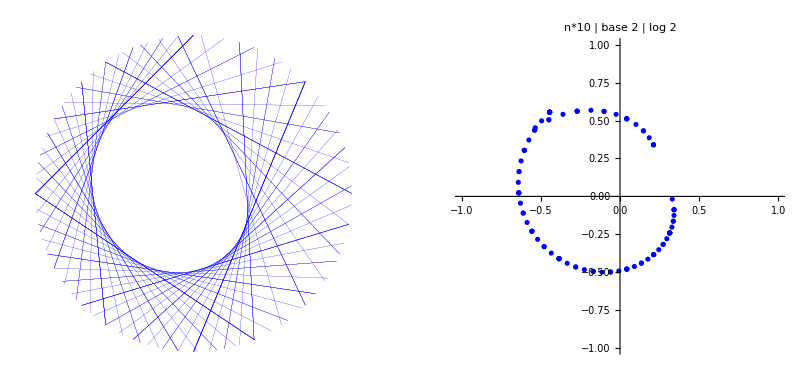

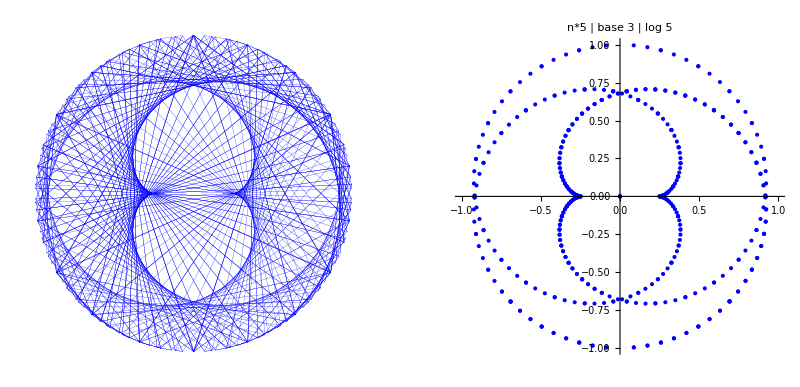

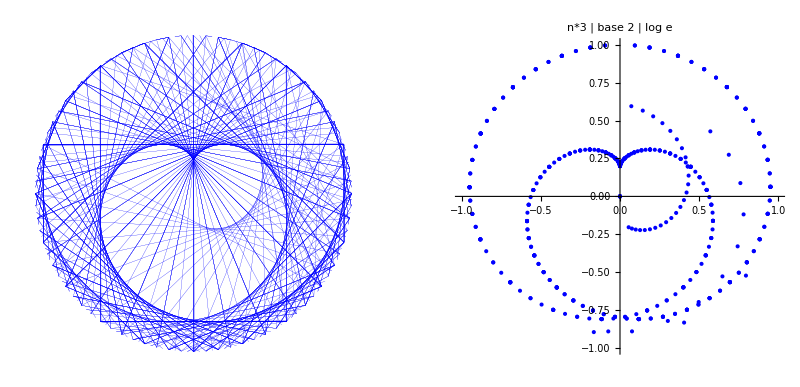

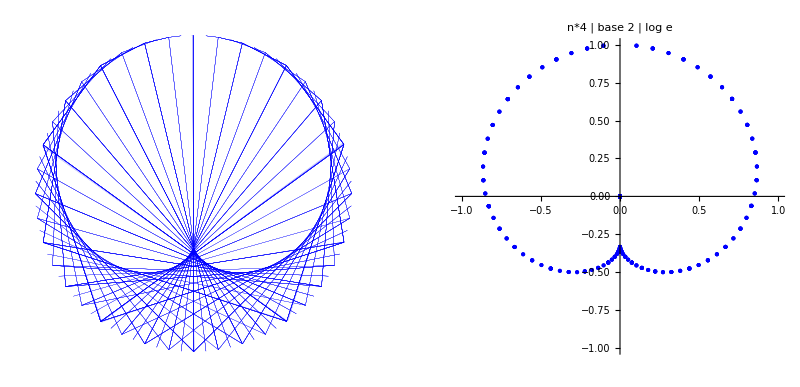

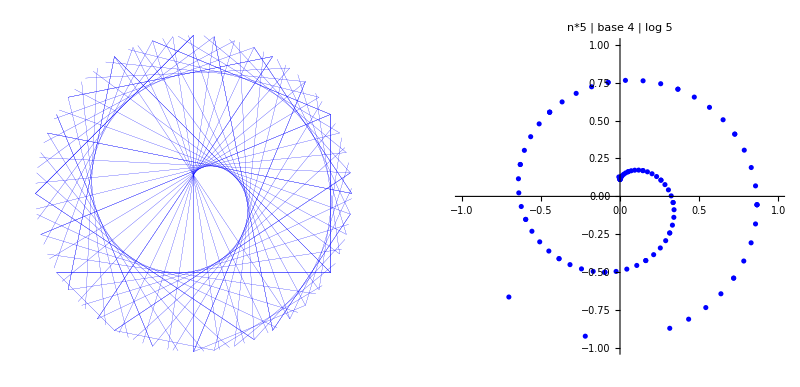

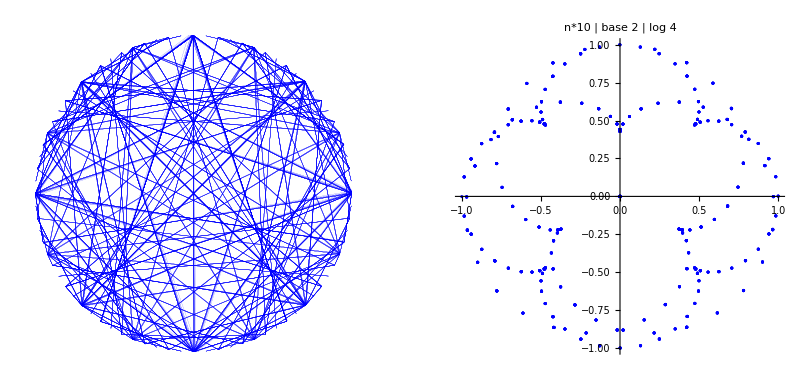

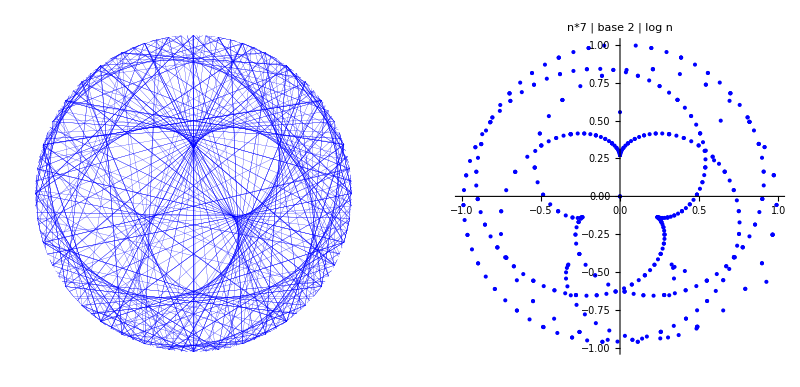

```mathematica
Remove[fnline,fnfact,rotate,intersect,intersectLines,start,stop,step,e];
rotate[n_]:=(alpha=2*Pi*fnfact[n];x=-Sin[alpha];y=Cos[alpha];{x,y});
(*intersect[n_,e_]:=(line1={rotate[n],rotate[fnline[n]]};line2={rotate[n+e],rotate[fnline[n+e]]};intersectLines[line1,line2,e]);*)

intersectLines[line1_,line2_]:=(
a11=line1[[1,2]]-line1[[2,2]];a12=line1[[2,1]]-line1[[1,1]];det1=Det[line1];a21=line2[[1,2]]-line2[[2,2]];a22=line2[[2,1]]-line2[[1,1]];det2=Det[line2];detx=Det[{{a12,det1},{a22,det2}}];dety=Det[{{det1,a11},{det2,a21}}];det=Det[{{a11,a12},{a21,a22}}];If[det>0,{detx/det,dety/det},{0,0}]);

generatePlot[fnline_,fnfact_, step_, label_]:= (
start=1;
stop=100;
e=0.001;
lines1=Table[{rotate[n],rotate[fnline[n]]},{n,start,stop,step}];
lines2=Table[{rotate[n+e],rotate[fnline[n+e]]},{n,start,stop,step}];
plot1=Graphics[{Blue, Thickness[0.0001],Append[Map[Line,lines1], Map[Line,lines2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label}];
plot2=ListPlot[MapThread[intersectLines,{lines1,lines2}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue];
GraphicsGrid[{{plot1,plot2}}]
);

fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,1, "n*7 | base 2 | log 2"]

fnline[n_]:=n*10;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,1, "n*10 | base 2 | log 2"]

fnline[n_]:=n*5;
fnfact[n_]:=n/(3^(Floor[Log[5,n]]+1)-3^Floor[Log[5,n]]);
generatePlot[fnline, fnfact,0.2, "n*5 | base 3 | log 5"]

fnline[n_]:=n*3;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
generatePlot[fnline, fnfact,0.2, "n*3 | base 2 | log e"]

fnline[n_]:=n*4;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
generatePlot[fnline, fnfact,0.2, "n*4 | base 2 | log e"]

fnline[n_]:=n*5;
fnfact[n_]:=n/(4^(Floor[Log[5,n]]+1)-4^Floor[Log[5,n]]);
generatePlot[fnline, fnfact,1, "n*5 | base 4 | log 5"]

fnline[n_]:=n*10;
fnfact[n_]:=n/(2^(Floor[Log[4,n]]+1)-2^Floor[Log[4,n]]);
generatePlot[fnline, fnfact,0.1, "n*10 | base 2 | log 4"]

fnline[n_]:=n*7;
fnfact[n_]:=n/(2^(Floor[Log[n]]+1)-2^Floor[Log[n]]);
generatePlot[fnline, fnfact,0.2, "n*7 | base 2 | log n"]

fnline[n_]:=n^3;
fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);
generatePlot[fnline, fnfact,0.3, "n^3 | base 2 | log 2"]

fnline[n_]:=2^n;
fnfact[n_]:=n/(3^(Floor[Log[3,n]]+1)-3^Floor[Log[3,n]]);
generatePlot[fnline, fnfact,0.25, "2^n | base 3 | log 3"]

fnline[n_]:=2^n;
fnfact[n_]:=n/(6^(Floor[Log[6,n]]+1)-6^Floor[Log[6,n]]);
generatePlot[fnline, fnfact,0.25, "2^n | base 3 | log 3"]
```